{{x→InterpolatingFunction[{{0.,5.}},<>]}}

-1.67814

21.7608

InterpolatingFunction[{{0.,5.}},<>][t]

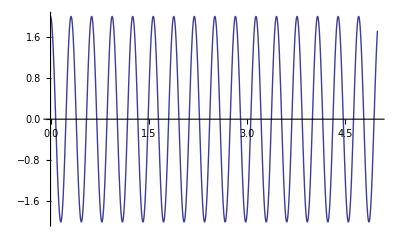

```mathematica
(*Solving SHO Problem NUMARICALLY *)
(*Pure Function: Readilly solvable and useable(Diff. Integrable.).
1):- while using DSolve and NDSolve , we donot use y[x] . we simply use 'y',with this we we'll be getting pure function sol. *)
ω=20;T=2Pi/ω;
deq=x''[t]+ω^2 x[t]==0;
(* Initial / boundary cond.s should be given.
( Behind NDSolve Command : Euler method,Euler chromer Algorithms are used.) 
sol. of NDSolve : is in the form of (Numarical values)InterpolatingFunction / Piecwise function:after using interpolation ,we get a function(Polynomial):'we can get value of independent varable by puttting any value of dependent variable(arbitrary variable.).
Sol. of NDSolve will be in either Numarical and Normal sol. form. *)
nsol=NDSolve[{deq,x'[0]==0,x[0]==2},x,{t,0,5}]
testvalue=x[0.5]/.nsol[[1]]
testvalue_at=x'[0.5]/.nsol[[1]]
nsol=x[i]/.nsol[[1]]
Plot[nsol,{i,0,5},PlotRange->All]
```

```mathematica
{{x->InterpolatingFunction[{{0.,5.}},"<>"]}}
```

-1.67814

21.7608

InterpolatingFunction[{{0.,5.}},<>]

```mathematica
??NDSolve
```

NDSolve[eqns,u,{t,t_min,t_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable t in the range t_min to t_max. 
NDSolve[eqns,u,{t,t_min,t_max},{x,x_min,x_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{u_1,u_2,…},{t,t_min,t_max}] finds numerical solutions for the functions u_i.

Attributes[NDSolve]={Protected}
 
Options[NDSolve]={AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→10000,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}